```mathematica
(*https://mathematica.stackexchange.com/questions/17121/adding-a-label-to-an-expression-result*)
SetAttributes[saveSet,HoldAll];
saveSet[form:Set[var_,_]]:=(lastSet=ToString@Unevaluated@var;form);
saveSet[form:___]:=(lastSet=.;form)

$Pre=saveSet;

$Post=(If[ValueQ@lastSet,Row[{lastSet," = ",#}],#])&;
```

Cost, gradients, Jacobian, and eigenvalues

```mathematica
f1=e x^4/4+a x^2/2 +  b x y
f2=d y^2/2+c x y
g1=D[f1,x]
g2=D[f2,y]
J=D[{-g1,-g2},{{x,y}}]
fixedpoints=Solve[{g1==0,g2==0},{x,y}]
eigvals=Eigenvalues[J]
eigvecs=Eigenvectors[J]
consts0={a->-1-e1,b->-1,c->2,d->1+e2,e->1};
```

f1 = (a x^2)/2+(e x^4)/4+b x y

f2 = c x y+(d y^2)/2

g1 = a x+e x^3+b y

g2 = c x+d y

J = {{-a-3 e x^2,-b},{-c,-d}}

fixedpoints = {{x→0,y→0},{x→-(√(b c-a d))/(√d √e),y→(c √(b c-a d))/(d^(3/2) √e)},{x→(√(b c-a d))/(√d √e),y→-(c √(b c-a d))/(d^(3/2) √e)}}

eigvals = {1/2 (-a-d-3 e x^2-√((a+d+3 e x^2)^2-4 (-b c+a d+3 d e x^2))),1/2 (-a-d-3 e x^2+√((a+d+3 e x^2)^2-4 (-b c+a d+3 d e x^2)))}

eigvecs = {{-(-a+d-3 e x^2-√(a^2+4 b c-2 a d+d^2+6 a e x^2-6 d e x^2+9 e^2 x^4))/(2 c),1},{-(-a+d-3 e x^2+√(a^2+4 b c-2 a d+d^2+6 a e x^2-6 d e x^2+9 e^2 x^4))/(2 c),1}}

Numerical simulation

(1.4 | 1
-2 | 4)

consts = {a→-1.1,b→-1,c→2,d→1.1,e→1}

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

g[x_] = {-1.1 x⟦1⟧+x⟦1⟧^3-x⟦2⟧,2 x⟦1⟧+1.1 x⟦2⟧}

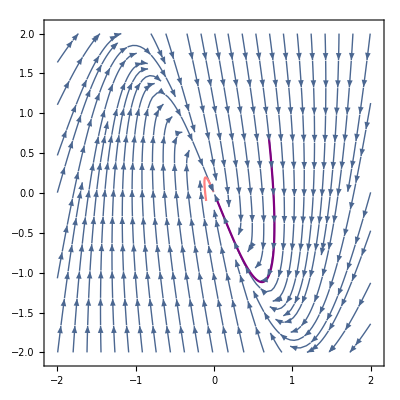

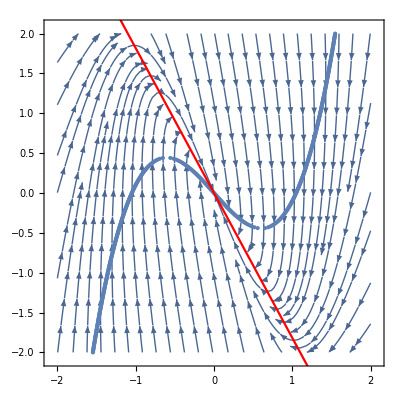

```mathematica
setup={e1->.1,e2->.1,γ1->.01,γ2->.05};
(*stable fixed point
{e1->.1,e2->.1,γ1->.01,γ2->.05}
stable limit cycle
{e1->.1,e2->.1,γ1->.05,γ2->.01}
two stable fixed points
{e1->.4,e2->5,γ1->.01,γ2->.01}
two unstable saddles
{e1->.4,e2->-5,γ1->.01,γ2->.01}
*)
J/.consts/.fixedpoints[[1]]//MatrixForm
consts=consts0/.setup
g[x_]={g1,g2}/.consts/.{x->x[[1]],y->x[[2]]}
numiter=300;
x0={{0.7,0.7},{-.1,-.1}};
γ={γ1,γ2}/.setup;


(*Simulate discrete system for two initial points*)
traj1=FoldList[#-γ*g[#]&,x0[[1]],Range[numiter]];
traj2=FoldList[#-γ*g[#]&,x0[[2]],Range[numiter]];

(*Plot continuous system vector field*)
lim=2;
streamplot=StreamPlot[{-γ[[1]]g1,-γ[[2]] g2}/.consts,{x,-lim,lim},{y,-lim,lim}];
Show[streamplot,
ListLinePlot[traj1,PlotStyle->{Purple}],
ListLinePlot[traj2,PlotStyle->{Pink}]]


(*Solve for best response curves*)
br1exact[y_]=Solve[γ1 g1==0,x][[All,1,2]];
br2exact[x_]=Solve[γ2 g2==0,y][[All,1,2]];
(*Choose only the real solutions*)
br1[y_]:=Select[Chop[br1exact[y]/.consts],Im[#]==0&];
br2[x_]=br2exact[x]/.consts;
tb=Table[ArrayFlatten[{br1[y],ConstantArray[y,Length[br1[y]]]}],{y,-lim,lim,.01}];
br1num=Transpose[{Catenate[tb[[All,1]]],Catenate[tb[[All,2]]]}];
br2num=Table[{x,br2[x][[1]]},{x,-lim,lim,.5}];

Show[streamplot,
ListPlot[br1num],
ListLinePlot[br2num,PlotStyle->Red]]
```